```mathematica
DataFileName="/Users/magse/workspace/pcb_layout_demo_eo/BRD1622204124540697.csv";
```

```mathematica
Timing[data=Import[DataFileName];]
```

{6.26278,Null}

```mathematica
ColorData["Physical"]
```

{BlackBodySpectrum,HypsometricTints,VisibleSpectrum}

```mathematica
LEDColor[r_]:=ColorData["Pastel",r/8.0]
```

```mathematica
PlotFrame[d_]:=Show[Graphics[{LightGreen,Annulus[{0,0},{20,90},{0,π/2}]},Axes->True],Graphics[Table[Partition[{Directive[EdgeForm[Thin],LEDColor[d⟦5+n⟧],Opacity[0.7]],Disk[{d⟦3+n⟧,d⟦4+n⟧},d⟦5+n⟧]},2],{n,1,Length[d]-4,3}],Axes->True],AspectRatio->1,PlotRange->{{0,100},{0,100}},Frame->True,FrameStyle->Directive[GrayLevel[0,0.2],Thickness[Medium],ImageSize->Large]]
```

```mathematica
PlotFrame[data⟦-1⟧]
```

-Graphics-

```mathematica
For[f=1,f<Length[data⟦All,1⟧],f=f+Length[data⟦All,1⟧]/10,Block[{frameplot=PlotFrame[data⟦f⟧]},Export[StringReplace[DataFileName,".csv"->"_"<>ToString[f]<>".pdf"],frameplot,"PDF","AllowRasterization"->False]]]
```

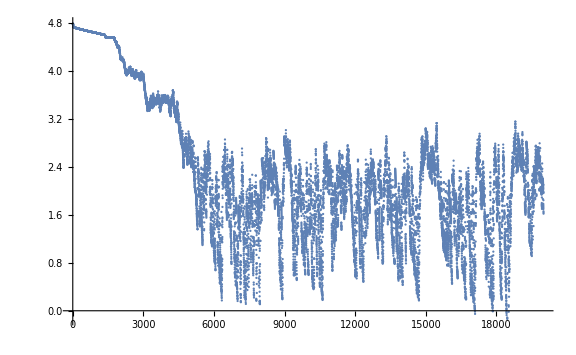

```mathematica
flawplot=ListPlot[Log[data⟦All,2⟧],PlotRange->All,ImageSize->Large]
```

```mathematica
Export[StringReplace[DataFileName,".csv"->"_flaws.pdf"],flawplot,"PDF","AllowRasterization"->False]
```

/Users/magse/workspace/pcb_layout_demo_eo/BRD1622203145982230_flaws.pdf

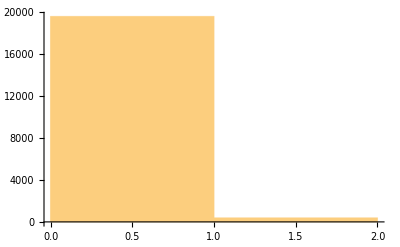

```mathematica
histplot=Histogram[data⟦All,3⟧,{1}]
```

```mathematica
Export[StringReplace[DataFileName,".csv"->"_hists.pdf"],histplot,"PDF","AllowRasterization"->False]
```

/Users/magse/workspace/pcb_layout_demo_eo/BRD1622203145982230_hists.pdf

```mathematica
Timing[Export[StringReplace[DataFileName,".csv"->".mov"],ListAnimate[Table[PlotFrame[data⟦n⟧],{n,1,Length[data⟦All,1⟧],100}],AnimationRate->12,ControlPlacement->Bottom, AppearanceElements->None]]]
```

{34.5671,/Users/magse/workspace/pcb_layout_demo_eo/BRD1622203145982230.mov}